```mathematica
(*Programm um die differentielle Zerfallsrate dΓ/ds34, die mit dG_Zc errechnet wurde, zu plotten.*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
(*Numerische Werte*)
lam=0.5;lamStep=0.05;eps=0.0005;epsStep=0.0005;mD=1.865;mDs=2.010;mZ=mDs+mD-eps;mPi=0.1396;mJ=3.0969;mGam=0;AlpFein=1/137;gJDD=7.44; gDsDPi=17.9;gDDsJPi=gJDD gDsDPi/(2Sqrt[2]);gZc=6.231382;q=Sqrt[4Pi AlpFein];g=Sqrt[6]gDDsJPi/((mZ^2-mJ^2)(1+mJ^2/(2mZ^2)));gZJPi=1;me=511.0 10^-6;mmu=105.6 10^-3;
```

```mathematica
(*Welche Datei soll geladen werden?*)
FileEps=500;
FileLam=500;
string0=StringJoin["dGamma2_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel0=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=5000;
FileLam=500;
string1=StringJoin["dGamma2_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel1=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=500;
FileLam=800;
string2=StringJoin["dGamma2_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel2=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=3000;
FileLam=650;
string3=StringJoin["dGamma2_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel3=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
FileEps=5000;
FileLam=800;
string4=StringJoin["dGamma2_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
plotlabel4=StringJoin["ϵ=",ToString[N[FileEps/1000]]," MeV\nΛ=",ToString[FileLam]," MeV"]
framelabel={"s_34 [GeV^2]","dΓ_4/ds_34 [GeV^-1]"}
```

dGamma2_eps500keV_lam500MeV.dat

ϵ=0.5 MeV
Λ=500 MeV

dGamma2_eps5000keV_lam500MeV.dat

ϵ=5. MeV
Λ=500 MeV

dGamma2_eps500keV_lam800MeV.dat

ϵ=0.5 MeV
Λ=800 MeV

dGamma2_eps3000keV_lam650MeV.dat

ϵ=3. MeV
Λ=650 MeV

dGamma2_eps5000keV_lam800MeV.dat

ϵ=5. MeV
Λ=800 MeV

{s_34 [GeV^2],dΓ_4/ds_34 [GeV^-1]}

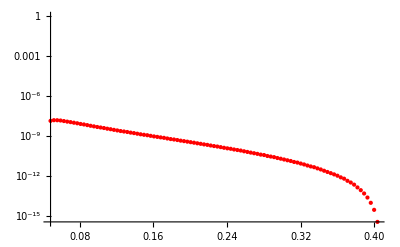
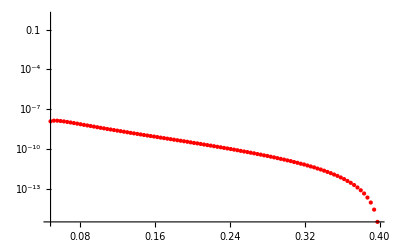
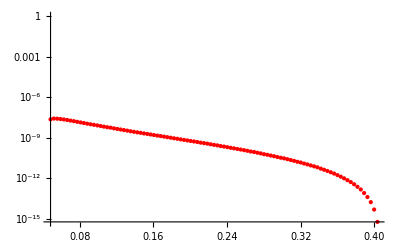
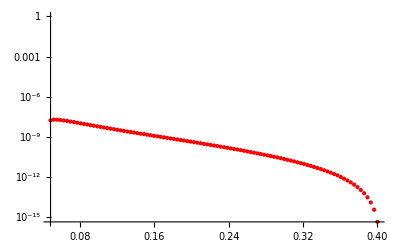
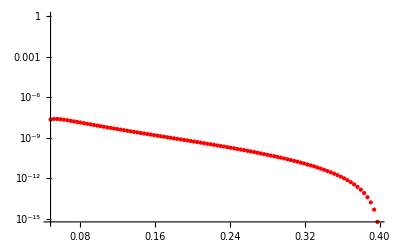

```mathematica
(*Datenwerte Laden, Duplikate aussortieren und fehlerhafte Einträge ignorieren*)
tG0=DeleteDuplicates[Delete[Cases[
Import[ToFileName[NotebookDirectory[],string0],"Table"],{_?NumberQ,_?NumberQ}],1]];
tG1=DeleteDuplicates[Delete[Cases[
Import[ToFileName[NotebookDirectory[],string1],"Table"],{_?NumberQ,_?NumberQ}],1]];
tG2=DeleteDuplicates[Delete[Cases[
Import[ToFileName[NotebookDirectory[],string2],"Table"],{_?NumberQ,_?NumberQ}],1]];
tG3=DeleteDuplicates[Delete[Cases[
Import[ToFileName[NotebookDirectory[],string3],"Table"],{_?NumberQ,_?NumberQ}],1]];
tG4=DeleteDuplicates[Delete[Cases[
Import[ToFileName[NotebookDirectory[],string4],"Table"],{_?NumberQ,_?NumberQ}],1]];
Row[{
ListLogPlot[tG0[[All,{1,2}]],PlotStyle->Directive[PointSize[Medium],Red]],
ListLogPlot[tG1[[All,{1,2}]],PlotStyle->Directive[PointSize[Medium],Red]],
ListLogPlot[tG2[[All,{1,2}]],PlotStyle->Directive[PointSize[Medium],Red]],
ListLogPlot[tG3[[All,{1,2}]],PlotStyle->Directive[PointSize[Medium],Red]],
ListLogPlot[tG4[[All,{1,2}]],PlotStyle->Directive[PointSize[Medium],Red]]}]
```

```mathematica
g0=tG0[[All, {1, 2}]] ;
g1=tG1[[All, {1, 2}]] ;
g2=tG2[[All, {1, 2}]] ;
g3=tG3[[All, {1, 2}]] ;
g4=tG4[[All, {1, 2}]] ;
```

```mathematica
ig0=Interpolation[g0,InterpolationOrder->1]
ig1=Interpolation[g1,InterpolationOrder->1]
ig2=Interpolation[g2,InterpolationOrder->1]
ig3=Interpolation[g3,InterpolationOrder->1]
ig4=Interpolation[g4,InterpolationOrder->1]
```

InterpolatingFunction[{{0.0482298,0.407044}},<>]

InterpolatingFunction[{{0.0481726,0.401322}},<>]

InterpolatingFunction[{{0.0482298,0.407044}},<>]

InterpolatingFunction[{{0.048198,0.40386}},<>]

InterpolatingFunction[{{0.0481726,0.401322}},<>]

```mathematica
(*Datenwerte interpolieren und integrieren*)
valGam0=NIntegrate[ig0[s34],{s34,(2mmu)^2,(mZ-mJ-mPi)^2}]1000000keV//Quiet
valGam1=NIntegrate[ig1[s34],{s34,(2mmu)^2,(mZ-mJ-mPi)^2}]1000000keV//Quiet
valGam2=NIntegrate[ig2[s34],{s34,(2mmu)^2,(mZ-mJ-mPi)^2}]1000000keV//Quiet
valGam3=NIntegrate[ig3[s34],{s34,(2mmu)^2,(mZ-mJ-mPi)^2}]1000000keV//Quiet
valGam4=NIntegrate[ig4[s34],{s34,(2mmu)^2,(mZ-mJ-mPi)^2}]1000000keV//Quiet
```

0.0095933 keV

0.00831149 keV

0.0160754 keV

0.0117944 keV

0.0153646 keV

```mathematica
PlotLegends->Placed[LineLegend[ley,LegendMarkers->Automatic,LegendMarkerSize->{{30,25}}],{After,Top}]
```

PlotLegends→Placed[LineLegend[ley,LegendMarkers→Automatic,LegendMarkerSize→{{30,25}}],{After,Top}]

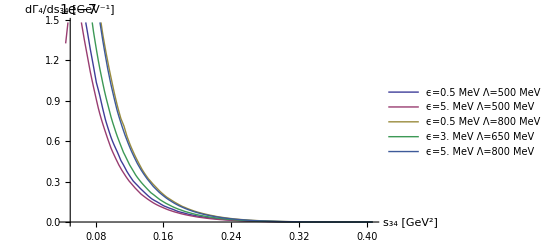

-Graphics-

```mathematica
(*Datenwerte plotten*)
Plot[{ig0[s34],ig1[s34],ig2[s34],ig3[s34],ig4[s34]},{s34,(2mmu)^2,(mZ-mJ-mPi)^2},AxesLabel->framelabel,PlotLegends->{Text[Style[plotlabel0,FontSize->11]],Text[Style[plotlabel1,FontSize->11]],Text[Style[plotlabel2,FontSize->11]],Text[Style[plotlabel3,FontSize->11]],Text[Style[plotlabel4,FontSize->11]]}]//Quiet
output=LogPlot[{
ig0[s34],
ig1[s34],
ig2[s34],
ig3[s34],
ig4[s34]},{s34,(2mmu)^2+0.008,(mZ-mJ-mPi)^2},
FrameLabel->framelabel,
LabelStyle->{FontSize->18},
PlotRange->{10^-15,10^-6},
PlotLegends->Placed[
LineLegend[
{Text[Style[plotlabel0,FontSize->13]],
Text[Style[plotlabel1,FontSize->13]],
Text[Style[plotlabel2,FontSize->13]],
Text[Style[plotlabel3,FontSize->13]],
Text[Style[plotlabel4,FontSize->13]]},
LegendLayout->{"Row",1}],{Above,Top}],
Frame->True,
Filling->{2->{{3},Directive[Opacity[0.2],Purple]}},
ImageSize->500]//Quiet
```

```mathematica
Export["dGammads34mu.eps",output,ImageResolution->400]
```

dGammads34mu.eps

```mathematica
(*Versuche ob aus den Werten dGDs12ds34 die selben Kurven durch Integration mit Mathematica folgen*)
FileEps=500;
FileLam=500;
string=StringJoin["dGamma_eps",ToString[FileEps],"keV_lam",ToString[FileLam],"MeV.dat"]
```

dGamma_eps500keV_lam500MeV.dat

```mathematica
(*Datenwerte Laden, Duplikate aussortieren und fehlerhafte Einträge ignorieren*)
tG=DeleteDuplicates[Delete[Cases[
Import[ToFileName[NotebookDirectory[],string],"Table"],{_,_,_}],1]];
ListPointPlot3D[tG[[All,{2,1,3}]],PlotStyle->Directive[PointSize[Medium],Red]]
```

-Graphics3D-

```mathematica
(*Interpolation*)
intG=Interpolation[tG,InterpolationOrder->1];
```

```mathematica
(*Datenwerte plotten*)
dGds34[s34_]:=NIntegrate[{intG[s12,s34]},{s12,(mJ+mPi)^2,(mZ-Sqrt[s34])^2}]
tdG=Table[{s34,dGds34[s34]},{s34,(2mmu)^2,(mZ-mJ-mPi)^2,0.005}]//Quiet;
```

```mathematica
idG=Interpolation[tdG,InterpolationOrder->1]
```

InterpolatingFunction[{{0.0446054,0.404605}},<>]

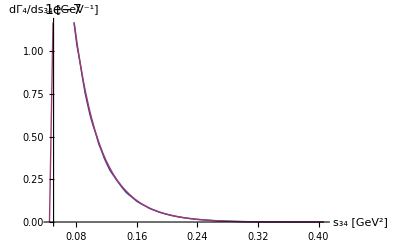

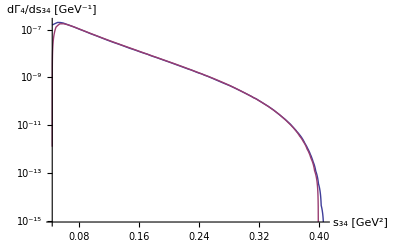

```mathematica
(*Datenwerte plotten*)
Plot[{ig0[s34],idG[s34]},{s34,(2mmu)^2,(mZ-mJ-mPi)^2},AxesLabel->framelabel]//Quiet
LogPlot[{ig0[s34],idG[s34]},{s34,(2mmu)^2,(mZ-mJ-mPi)^2},AxesLabel->framelabel]//Quiet
```